# Daavid 2016 fig1: Symmetric MNR with adiabatic approximation and analytic prediction To keep the simpilicity, we use Δ as the Vacuum Scale. Use Δ = 1 for normal hierarchy. Use μ_ν=10000Δ as inteaction strenth. Mixing angle θ_13=0.154. Asymmetry α=a+b*r, where a= 1.3, b= -0.048 Constant matter potential: V_e=1000Δ

```mathematica
Δ:=1;
μ[r_]:=10000*Δ*Exp[-r/10];
θ13:=0.154;
a=1.3;
b=-0.048;
α[r_]:=4./3.;
cc=2.99792458*^10; (* c in cgs, cm/s*)
hbar=1.05457266*^-27; (*erg s*)
gNu=cc/((hbar*cc)^3);
eV=1.6021772*^-12; (* erg*)
rmax=45;
```

## Then all the potentials,

{-0.303153,0,0.952942}

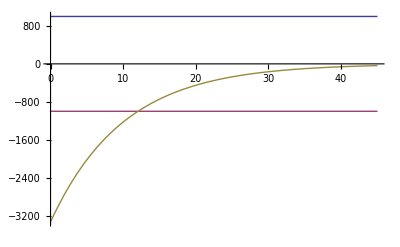

```mathematica
V={-Sin[2*θ13],0,Cos[2*θ13]}*Δ
Ve[r_]:={0,0,1000}*Δ
Hnn[r_]:=-(α[r]-1)*μ[r]
R[r_]:=Ve[r][[3]]/μ[r]
Plot[{(Ve[r])[[3]],-(Ve[r])[[3]],Hnn[r]},{r,0,rmax},PlotRange->All]
```

```mathematica
CP=Solve[(Ve[r])[[3]]+Hnn[r]==0,r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→12.0397}}

### So the cancelation point is at CP

### Let’s solve the evalution in Isospin

{2.664,{{M1→InterpolatingFunction[{{0.,50.}},<>],M2→InterpolatingFunction[{{0.,50.}},<>]}}}

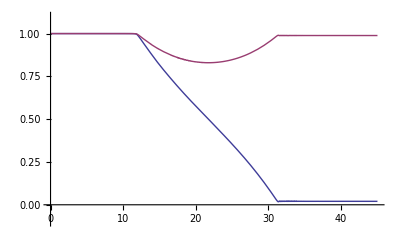

```mathematica
Timing[sol=NDSolve[{M1'[r]==Cross[M1[r],V+Ve[r]]+2*μ[r]*Cross[M1[r],α[r]*M2[r]],M2'[r]==Cross[M2[r],-V+Ve[r]]+2*μ[r]*Cross[M2[r],M1[r]],M1[0]=={0,0,0.5},M2[0]=={0,0,-0.5}},{M1,M2},{r,0,50},MaxSteps->10000000]]
Plot[{0.5+(M1[r]/.sol)[[1,3]],0.5-(M2[r]/.sol)[[1,3]]},{r,0,rmax},PlotRange->{{0,rmax},{-0.1,1.1}}]
```

### Predictions 1. Where the MNR starts and ends. Ref[Malkus 2014], ri @Ve[r])[[3]]+(1-α[r])*μ==0, rf@Ve[r])[[3]]+(1+α[r])*μ==0, Why not working here? 2. How the Survival probability is like? -Graphics-

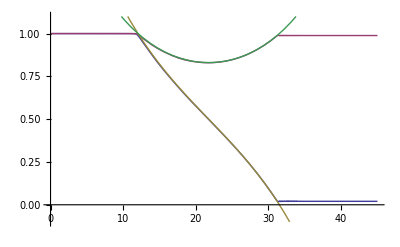

```mathematica
Pnue[r_]:=0.5(1+(α[r]^2 - R[r]^2 - 1)/(2*R[r]))
Panue[r_]:=0.5(1+(α[r]^2 + R[r]^2 - 1)/(2*α[r]*R[r]))
Plot[{0.5+(M1[r]/.sol)[[1,3]],0.5-(M2[r]/.sol)[[1,3]],Pnue[r],Panue[r]},{r,0,rmax},PlotRange->{{0,rmax},{-0.1,1.1}}]
```